```mathematica
AppendTo[$Path,NotebookDirectory[] <> "../src/"];
<<affine.m;
```

```mathematica
OverHat[Subscript[A, 2]][gradeLimit]=3
```

3

```mathematica
ch2=Flatten[Outer[{Plus[##],Inner[(#1@#2)&,{ch1,ch1},{##},Times]}&,Sequence@@((#[weights])&/@{ch1,ch1}),1],1];
```

```mathematica
94*94
```

8836

```mathematica
OverHat[Subscript[A, 1]]
```

affineRootSystem[1,finiteRootSystem[1,1,{finiteWeight[1,{√2}]}],affineWeight[1,finiteWeight[1,{-√2}],0,1],{affineWeight[1,finiteWeight[1,{√2}],0,0]}]

```mathematica
roots[makeAffineExtension[makeFiniteRootSystem[{finiteWeight[1,{√2}],finiteWeight[1,{√2}]}]]]
```

{affineWeight[1,finiteWeight[1,{0}],0,-11],affineWeight[1,finiteWeight[1,{0}],0,-10],affineWeight[1,finiteWeight[1,{0}],0,-9],affineWeight[1,finiteWeight[1,{0}],0,-8],affineWeight[1,finiteWeight[1,{0}],0,-7],affineWeight[1,finiteWeight[1,{0}],0,-6],affineWeight[1,finiteWeight[1,{0}],0,-5],affineWeight[1,finiteWeight[1,{0}],0,-4],affineWeight[1,finiteWeight[1,{0}],0,-3],affineWeight[1,finiteWeight[1,{0}],0,-2],affineWeight[1,finiteWeight[1,{0}],0,-1],affineWeight[1,finiteWeight[1,{0}],0,1],affineWeight[1,finiteWeight[1,{0}],0,2],affineWeight[1,finiteWeight[1,{0}],0,3],affineWeight[1,finiteWeight[1,{0}],0,4],affineWeight[1,finiteWeight[1,{0}],0,5],affineWeight[1,finiteWeight[1,{0}],0,6],affineWeight[1,finiteWeight[1,{0}],0,7],affineWeight[1,finiteWeight[1,{0}],0,8],affineWeight[1,finiteWeight[1,{0}],0,9],affineWeight[1,finiteWeight[1,{0}],0,10],affineWeight[1,finiteWeight[1,{0}],0,11],affineWeight[1,finiteWeight[1,{-√2}],0,-10],affineWeight[1,finiteWeight[1,{-√2}],0,-9],affineWeight[1,finiteWeight[1,{-√2}],0,-8],affineWeight[1,finiteWeight[1,{-√2}],0,-7],affineWeight[1,finiteWeight[1,{-√2}],0,-6],affineWeight[1,finiteWeight[1,{-√2}],0,-5],affineWeight[1,finiteWeight[1,{-√2}],0,-4],affineWeight[1,finiteWeight[1,{-√2}],0,-3],affineWeight[1,finiteWeight[1,{-√2}],0,-2],affineWeight[1,finiteWeight[1,{-√2}],0,-1],affineWeight[1,finiteWeight[1,{-√2}],0,0],affineWeight[1,finiteWeight[1,{-√2}],0,1],affineWeight[1,finiteWeight[1,{-√2}],0,2],affineWeight[1,finiteWeight[1,{-√2}],0,3],affineWeight[1,finiteWeight[1,{-√2}],0,4],affineWeight[1,finiteWeight[1,{-√2}],0,5],affineWeight[1,finiteWeight[1,{-√2}],0,6],affineWeight[1,finiteWeight[1,{-√2}],0,7],affineWeight[1,finiteWeight[1,{-√2}],0,8],affineWeight[1,finiteWeight[1,{-√2}],0,9],affineWeight[1,finiteWeight[1,{-√2}],0,10],affineWeight[1,finiteWeight[1,{√2}],0,-10],affineWeight[1,finiteWeight[1,{√2}],0,-9],affineWeight[1,finiteWeight[1,{√2}],0,-8],affineWeight[1,finiteWeight[1,{√2}],0,-7],affineWeight[1,finiteWeight[1,{√2}],0,-6],affineWeight[1,finiteWeight[1,{√2}],0,-5],affineWeight[1,finiteWeight[1,{√2}],0,-4],affineWeight[1,finiteWeight[1,{√2}],0,-3],affineWeight[1,finiteWeight[1,{√2}],0,-2],affineWeight[1,finiteWeight[1,{√2}],0,-1],affineWeight[1,finiteWeight[1,{√2}],0,0],affineWeight[1,finiteWeight[1,{√2}],0,1],affineWeight[1,finiteWeight[1,{√2}],0,2],affineWeight[1,finiteWeight[1,{√2}],0,3],affineWeight[1,finiteWeight[1,{√2}],0,4],affineWeight[1,finiteWeight[1,{√2}],0,5],affineWeight[1,finiteWeight[1,{√2}],0,6],affineWeight[1,finiteWeight[1,{√2}],0,7],affineWeight[1,finiteWeight[1,{√2}],0,8],affineWeight[1,finiteWeight[1,{√2}],0,9],affineWeight[1,finiteWeight[1,{√2}],0,10]}

```mathematica
Length[roots[makeAffineExtension[makeFiniteRootSystem[{finiteWeight[1,{√2}]}]]]]
```

64

```mathematica
rts=Flatten[Outer[{Plus[##],Inner[(#1@#2)&,{ch1,ch1},{##},Times]}&,Sequence@@((#[weights])&/@{ch1,ch1}),1],1];
```

```mathematica
Length[ch2]
```

8836

```mathematica
genericBranching[OverHat[Subscript[A, 2]],Plus,{makeIrreducibleModule[OverHat[Subscript[A, 2]]][1,1,1],makeIrreducibleModule[OverHat[Subscript[A, 2]]][1,1,1]}][multiplicities]
```

```mathematica
ch1=character[makeIrreducibleModule[OverHat[Subscript[A, 2]]][1,1,1]]
```

formalElement[Affine`Private`table$1483]

```mathematica
Length[ch1[weights]]
```

94

```mathematica
fun[ls_:{0,1}]:=Module[{},Plus@@ls]
```

```mathematica
fun[{1,2,3}]
```

```mathematica
fun@@{1,2,3}
```

```mathematica
Outer[Plus,{{1,2},{3,4}},2]
```

{{1,2},{3,4}}

```mathematica
(Plus@@#)&@{1,2,3}
```

6

```mathematica
?Apply
```

Apply[f,expr] or f@@expr replaces the head of expr by f. 
Apply[f,expr,levelspec] replaces heads in parts of expr specified by levelspec.

```mathematica
?@
```

```mathematica
?Plus
```

RowBox[{StyleBox["x", "TI"], "+", StyleBox["y", "TI"], "+", StyleBox["z", "TI"]}] represents a sum of terms. 
 It is defined for weights of finite and affine Lie algebras

```mathematica
?Times
```

x*y*z, x×y×z or x y z represents a product of terms. 

 Mutliplication by numbers is defined for the elements of weight space of affine and finite-dimensional Lie algebras. 
    
 For example makeFiniteWeight[{1,2,3}]*2==makeFiniteWeight[{2,4,6}]]

```mathematica
?Outer
```

RowBox[{"Outer", "[", RowBox[{StyleBox["f", "TI"], ",", SubscriptBox[StyleBox["list", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["list", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "]"}] gives the generalized outer product of the SubscriptBox[StyleBox["list", "TI"], StyleBox["i", "TI"]], forming all possible combinations of the lowest-level elements in each of them, and feeding them as arguments to StyleBox["f", "TI"]. 
RowBox[{"Outer", "[", RowBox[{StyleBox["f", "TI"], ",", SubscriptBox[StyleBox["list", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["list", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"], ",", StyleBox["n", "TI"]}], "]"}] treats as separate elements only sublists at level StyleBox["n", "TI"] in the SubscriptBox[StyleBox["list", "TI"], StyleBox["i", "TI"]]. 
RowBox[{"Outer", "[", RowBox[{StyleBox["f", "TI"], ",", SubscriptBox[StyleBox["list", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["list", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"], ",", SubscriptBox[StyleBox["n", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["n", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "]"}] treats as separate elements only sublists at level SubscriptBox[StyleBox["n", "TI"], StyleBox["i", "TI"]] in the corresponding SubscriptBox[StyleBox["list", "TI"], StyleBox["i", "TI"]].

```mathematica
Through[{f1,f2,f3}[1]]
```

{f1[1],f2[1],f3[1]}

```mathematica
?Through
```

Through[p[f_1,f_2][x]] gives p[f_1[x],f_2[x]]. 
Through[expr,h] performs the transformation wherever h occurs in the head of expr.

```mathematica
?Apply
```

Apply[f,expr] or f@@expr replaces the head of expr by f. 
Apply[f,expr,levelspec] replaces heads in parts of expr specified by levelspec.

```mathematica
Subscript[A, 1][gradeLimit]
```

10

```mathematica
weight[Subscript[A, 1]][1]
```

finiteWeight[1,{1/(√2)}]

```mathematica
genericBranching[subs_?rootSystemQ,pr_,{ms__module}]:=
Module[{characters,wgs,res,pmults,rh},
characters=character/@{ms};
pmults=makeFormalElement@@Transpose[
Select[
Flatten[Outer[{pr[##],Inner[(#1@#2)&,characters,{##},Times]}&,
Sequence@@((#[weights])&/@characters),1],1],
grade[#[[1]]]+subs[gradeLimit]≥0&]];
res=makeFormalElement[makeHashtable[{},{}]];
rh=rho[subs];
wgs=Select[Sort[pmults[weights],#1.rh>#2.rh&],mainChamberQ[subs]];
Scan[(res[hashtable][#]=pmults[#];pmults=pmults-pmults[#]*racahMultiplicities[subs][#])&,wgs];
res]
```

```mathematica
?Map
```

Map[f,expr] or f/@expr applies f to each element on the first level in expr. 
Map[f,expr,levelspec] applies f to parts of expr specified by levelspec.

```mathematica
ch=character[makeIrreducibleModule[Subscript[A, 1]][1]]
```

formalElement[Affine`Private`table$10470]

```mathematica
FullForm[##&]
```

Function[SlotSequence[1]]

```mathematica
Apply[ch,{weight[Subscript[A, 1]][1]}]
```

1

```mathematica
f1[1]
```

f1[1]

```mathematica
f1@@1
```

1

```mathematica
Apply[f1,1]
```

1

```mathematica
Outer[{##}&,{f1,f2,f3},{1,2,3}]
```

{{{f1,1},{f1,2},{f1,3}},{{f2,1},{f2,2},{f2,3}},{{f3,1},{f3,2},{f3,3}}}

```mathematica
?Inner
```

RowBox[{"Inner", "[", RowBox[{StyleBox["f", "TI"], ",", SubscriptBox[StyleBox["list", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["list", "TI"], StyleBox["2", "TR"]], ",", StyleBox["g", "TI"]}], "]"}] is a generalization of Dot in which StyleBox["f", "TI"] plays the role of multiplication and StyleBox["g", "TI"] of addition.

```mathematica
genericBranching[subs_?rootSystemQ,pr_,{ms__module}]:=
Module[{characters,wgs,res,pmults,rh},
characters=character/@{ms};
Outer[{pr[##],Inner[(#1@#2)&,characters,{##},Times]}&,
Sequence@@((#[weights])&/@characters),1]]
```

```mathematica
?Outer
```

Outer[
StyleBox["f", "TI"], SubscriptBox[
StyleBox["list", "TI"], 
StyleBox["1", "TR"]], SubscriptBox[
StyleBox["list", "TI"], 
StyleBox["2", "TR"]], 
StyleBox["…", "TR"]] gives the generalized outer product of the SubscriptBox[
StyleBox["list", "TI"], 
StyleBox["i", "TI"]], forming all possible combinations of the lowest-level elements in each of them, and feeding them as arguments to 
StyleBox["f", "TI"]. \nOuter[
StyleBox["f", "TI"], SubscriptBox[
StyleBox["list", "TI"], 
StyleBox["1", "TR"]], SubscriptBox[
StyleBox["list", "TI"], 
StyleBox["2", "TR"]], 
StyleBox["…", "TR"], 
StyleBox["n", "TI"]] treats as separate elements only sublists at level 
StyleBox["n", "TI"] in the SubscriptBox[
StyleBox["list", "TI"], 
StyleBox["i", "TI"]]. \nOuter[
StyleBox["f", "TI"], SubscriptBox[
StyleBox["list", "TI"], 
StyleBox["1", "TR"]], SubscriptBox[
StyleBox["list", "TI"], 
StyleBox["2", "TR"]], 
StyleBox["…", "TR"], SubscriptBox[
StyleBox["n", "TI"], 
StyleBox["1", "TR"]], SubscriptBox[
StyleBox["n", "TI"], 
StyleBox["2", "TR"]], 
StyleBox["…", "TR"]] treats as separate elements only sublists at level SubscriptBox[
StyleBox["n", "TI"], 
StyleBox["i", "TI"]] in the corresponding SubscriptBox[
StyleBox["list", "TI"], 
StyleBox["i", "TI"]].

```mathematica
Outer[f,Sequence@@((#[weights])&/@character/@{makeIrreducibleModule[Subscript[A, 1]][1],makeIrreducibleModule[Subscript[A, 1]][2]}),1]
```

{{f[finiteWeight[1,{1/(√2)}],finiteWeight[1,{√2}]],f[finiteWeight[1,{1/(√2)}],finiteWeight[1,{-√2}]],f[finiteWeight[1,{1/(√2)}],finiteWeight[1,{0}]]},{f[finiteWeight[1,{-1/(√2)}],finiteWeight[1,{√2}]],f[finiteWeight[1,{-1/(√2)}],finiteWeight[1,{-√2}]],f[finiteWeight[1,{-1/(√2)}],finiteWeight[1,{0}]]}}

```mathematica
?Function
```

Function[body] or body& is a pure function. The formal parameters are # (or #1), #2, etc. 
Function[x,body] is a pure function with a single formal parameter x. 
Function[{x_1,x_2,…},body] is a pure function with a list of formal parameters.

```mathematica
Outer[Function[{x},{x}],Sequence@@((#[weights])&/@character/@{makeIrreducibleModule[Subscript[A, 1]][1],makeIrreducibleModule[Subscript[A, 1]][2]}),1]
```

{{{finiteWeight[1,{1/(√2)}]},{finiteWeight[1,{1/(√2)}]},{finiteWeight[1,{1/(√2)}]}},{{finiteWeight[1,{-1/(√2)}]},{finiteWeight[1,{-1/(√2)}]},{finiteWeight[1,{-1/(√2)}]}}}

{{finiteWeight[1,{3/(√2)}],finiteWeight[1,{-1/(√2)}],finiteWeight[1,{1/(√2)}]},{finiteWeight[1,{1/(√2)}],finiteWeight[1,{-3/(√2)}],finiteWeight[1,{-1/(√2)}]}}

```mathematica
Outer[List,Sequence@@{{1,2},{3,4,5}},1]
```

{{{1,3},{1,4},{1,5}},{{2,3},{2,4},{2,5}}}

```mathematica
{makeIrreducibleModule[Subscript[A, 1]][1],makeIrreducibleModule[Subscript[A, 1]][1]}
```

{module[finiteRootSystem[1,1,{finiteWeight[1,{√2}]}],formalElement[Affine`Private`table$10386],finiteRootSystem[1,1,{finiteWeight[1,{√2}]}],10],module[finiteRootSystem[1,1,{finiteWeight[1,{√2}]}],formalElement[Affine`Private`table$10388],finiteRootSystem[1,1,{finiteWeight[1,{√2}]}],10]}

```mathematica
genericBranching[Subscript[A, 1],Plus,{makeIrreducibleModule[Subscript[A, 1]][2],makeIrreducibleModule[Subscript[A, 1]][2],makeIrreducibleModule[Subscript[A, 1]][5]}][multiplicities]
```

Transpose::nmtx: The first two levels of the one-dimensional list {} cannot be transposed.

DownValues::sym: Argument {} at position 1 is expected to be a symbol.

Part::partw: Part 1 of {} does not exist.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

{}

```mathematica
minimalCharactersGen[{ls1__Integer},ls2_:{0,1}]:=Module[{
a1a=makeAffineExtension[makeSimpleRootSystem[A,1]],ch1,ch2,wgs,res,pmults,subs,rh},
a1a[gradeLimit]=5;
res=genericBranching[a1a,Plus,{makeIrreducibleModule[a1a][ls1],makeIrreducibleModule[a1a]@@ls2}];
{conformalWeight[weight[a1a][ls1]]+conformalWeight[weight[a1a]@@ls2]-conformalWeight[#],Affine`Private`stringSelector[res,#,8]}&/@Select[res[weights],grade[#]==0&]]
```

```mathematica
minimalCharactersGen[{0,1}]
```

{{0,1+q^2+q^3+2 q^4+2 q^5},{1/2,1+q+q^2+q^3+2 q^4+2 q^5}}

```mathematica
minimalCharacters[{ls1__Integer},ls2_:{0,1}]:=
Module[{
a1a=makeAffineExtension[makeSimpleRootSystem[A,1]],ch1,ch2,wgs,res,pmults,subs,rh},
a1a[gradeLimit]=5;
ch1=character[makeIrreducibleModule[a1a][ls1]];
ch2=character[makeIrreducibleModule[a1a]@@ls2];
pmults=makeFormalElement@@Transpose[Select[Flatten[Outer[{#1+#2,ch1[#1]*ch2[#2]}&,ch1[weights],ch2[weights]],1],-grade[#[[1]]]≤a1a[gradeLimit]&]];
subs=a1a;
res=makeFormalElement[makeHashtable[{},{}]];
rh=rho[subs];
wgs=Select[Sort[pmults[weights],#1.rh>#2.rh&],mainChamberQ[subs]];
Scan[(res[hashtable][#]=pmults[#];pmults=pmults-pmults[#]*racahMultiplicities[subs][#])&,wgs];
{conformalWeight[weight[a1a][ls1]]+conformalWeight[weight[a1a]@@ls2]-conformalWeight[#],Affine`Private`stringSelector[res,#,8]}&/@Select[res[weights],grade[#]==0&]]
```

```mathematica
minimalCharacters[{0,1}]
```

{{0,1+q^2+q^3+2 q^4+2 q^5+3 q^6+3 q^7+5 q^8},{1/2,1+q+q^2+q^3+2 q^4+2 q^5+3 q^6+4 q^7+5 q^8}}

```mathematica
minimalCharacters[{0,1},{1,0}]
```

{{1/16,1+q+q^2+2 q^3+2 q^4+3 q^5+4 q^6+5 q^7+6 q^8}}

```mathematica
minimalCharacters[{1,0},{1,0}]
```

{{0,1+q^2+q^3+2 q^4+2 q^5+3 q^6+3 q^7+5 q^8}}

```mathematica
minimalCharacters[{0,2}]
```

{{0,1+q^2+q^3+2 q^4+2 q^5+4 q^6+4 q^7+7 q^8},{3/5,1+q+2 q^2+2 q^3+4 q^4+5 q^5+7 q^6+9 q^7+13 q^8}}

```mathematica
minimalCharacters[{1,1}]
```

{{3/80,1+q+2 q^2+3 q^3+4 q^4+6 q^5+8 q^6+11 q^7+15 q^8},{7/16,1+q+q^2+2 q^3+3 q^4+4 q^5+6 q^6+8 q^7+10 q^8}}

```mathematica
minimalCharacters[{2,0}]
```

{{1/10,1+q+q^2+2 q^3+3 q^4+4 q^5+6 q^6+8 q^7+11 q^8}}

```mathematica
minimalCharacters[{2,0},{1,0}]
```

{{0,1+q^2+q^3+2 q^4+2 q^5+4 q^6+4 q^7+7 q^8}}

```mathematica
minimalCharacters[{1,1},{1,0}]
```

{{3/80,1+q+2 q^2+3 q^3+4 q^4+6 q^5+8 q^6+11 q^7+15 q^8}}

```mathematica
minimalCharacters[{2,0},{1,0}]
```

{{1/10,1+q+q^2+2 q^3+3 q^4+4 q^5+6 q^6+8 q^7+11 q^8},{1/2,q+q^2+2 q^3+2 q^4+3 q^5+4 q^6+6 q^7+7 q^8}}

```mathematica
minimalCharacters[{3,0}]
```

{{1/8,1+q+q^2+2 q^3+3 q^4+4 q^5+6 q^6+8 q^7+11 q^8}}

```mathematica
minimalCharacters[{2,1}]
```

$Aborted

```mathematica
minimalCharacters[{1,2}]
```

{{1/40,1+q+2 q^2+3 q^3+4 q^4+6 q^5+9 q^6+12 q^7+17 q^8},{21/40,1+q+2 q^2+3 q^3+5 q^4+7 q^5+10 q^6+14 q^7+19 q^8}}

```mathematica
minimalCharacters[{0,3},{1,0}]
```

{{5/8,q+q^2+2 q^3+3 q^4+4 q^5+6 q^6+9 q^7+12 q^8},{1/8,1+q+q^2+2 q^3+3 q^4+4 q^5+6 q^6+8 q^7+11 q^8}}

```mathematica
minimalCharacters[{2,1},{1,0}]
```

{{1/40,1+q+2 q^2+3 q^3+4 q^4+6 q^5+9 q^6+12 q^7+17 q^8}}

```mathematica
minimalCharacters[{0,3}]
```

{{1,q^2+q^3+2 q^4+3 q^5},{2/3,1+q+2 q^2+2 q^3+4 q^4+5 q^5},{0,1+q^2+q^3+2 q^4+2 q^5}}

```mathematica
minimalCharactersGen[{0,3}]
```

{{1,q^2+q^3+2 q^4+3 q^5},{0,1+q^2+q^3+2 q^4+2 q^5},{2/3,1+q+2 q^2+2 q^3+4 q^4+5 q^5}}

```mathematica
minimalCharacters[{2,1}]
```

{{1/15,1+q+2 q^2+3 q^3+5 q^4+7 q^5},{2/5,1+q+q^2+2 q^3+3 q^4+4 q^5}}

```mathematica
minimalCharacters[{1,2}]
```

{{1/40,1+q+2 q^2+3 q^3+4 q^4+6 q^5},{21/40,1+q+2 q^2+3 q^3+5 q^4+7 q^5}}

```mathematica
minimalCharacters[{3,0},{1,0}]
```

{{0,1+q^2+q^3+2 q^4+2 q^5}}

```mathematica
minimalCharacters[{2,1},{1,0}]
```

{{1/40,1+q+2 q^2+3 q^3+4 q^4+6 q^5}}

```mathematica
minimalCharacters[{1,2},{1,0}]
```

{{1/15,1+q+2 q^2+3 q^3+5 q^4+7 q^5},{2/5,q+q^2+2 q^3+2 q^4+4 q^5}}

```mathematica
minimalCharacters[{0,3},{1,0}]
```

{{1/8,1+q+q^2+2 q^3+3 q^4+4 q^5},{5/8,q+q^2+2 q^3+3 q^4+4 q^5}}

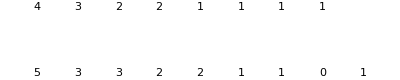

```mathematica
a1a=makeAffineExtension[makeSimpleRootSystem[A,1]];
a1a[gradeLimit]=8;
mod1=makeIrreducibleModule[a1a][1,0];
mod2=makeIrreducibleModule[a1a][1,0];
ch1=character[mod1];
ch2=character[mod2];
pmults=makeFormalElement@@Transpose[Select[Flatten[Outer[{#1+#2,ch1[#1]*ch2[#2]}&,ch1[weights],ch2[weights]],1],-grade[#[[1]]]≤a1a[gradeLimit]&]];
subs=a1a;
res=makeFormalElement[makeHashtable[{},{}]];
rh=rho[subs];
wgs=Select[Sort[pmults[weights],#1.rh>#2.rh&],mainChamberQ[subs]];
Scan[(res[hashtable][#]=pmults[#];pmults=pmults-pmults[#]*racahMultiplicities[subs][#])&,wgs];
affinePlot[res]
```

```mathematica
a1a=makeAffineExtension[makeSimpleRootSystem[A,1]];
a1a[gradeLimit]=8;
mod1=makeIrreducibleModule[a1a][0,1];
mod2=makeIrreducibleModule[a1a][1,0];
ch1=character[mod1];
ch2=character[mod2];
pmults=makeFormalElement@@Transpose[Select[Flatten[Outer[{#1+#2,ch1[#1]*ch2[#2]}&,ch1[weights],ch2[weights]],1],-grade[#[[1]]]≤a1a[gradeLimit]&]];
subs=a1a;
res=makeFormalElement[makeHashtable[{},{}]];
rh=rho[subs];
wgs=Select[Sort[pmults[weights],#1.rh>#2.rh&],mainChamberQ[subs]];
Scan[(res[hashtable][#]=pmults[#];pmults=pmults-pmults[#]*racahMultiplicities[subs][#])&,wgs];
affinePlot[res]
```

-Graphics-

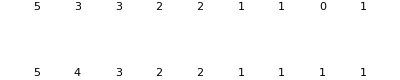

```mathematica
a1a=makeAffineExtension[makeSimpleRootSystem[A,1]];
a1a[gradeLimit]=8;
mod1=makeIrreducibleModule[a1a][0,1];
mod2=makeIrreducibleModule[a1a][0,1];
ch1=character[mod1];
ch2=character[mod2];
pmults=makeFormalElement@@Transpose[Select[Flatten[Outer[{#1+#2,ch1[#1]*ch2[#2]}&,ch1[weights],ch2[weights]],1],-grade[#[[1]]]≤a1a[gradeLimit]&]];
subs=a1a;
res=makeFormalElement[makeHashtable[{},{}]];
rh=rho[subs];
wgs=Select[Sort[pmults[weights],#1.rh>#2.rh&],mainChamberQ[subs]];
Scan[(res[hashtable][#]=pmults[#];pmults=pmults-pmults[#]*racahMultiplicities[subs][#])&,wgs];
affinePlot[res]
```

```mathematica
affinePlot[f_formalElement,opts___?OptionQ]:=
Graphics[(Text[f[#],{grade[#],#[finitePart][standardBase][[1]]}]&)/@f[weights],opts]
```

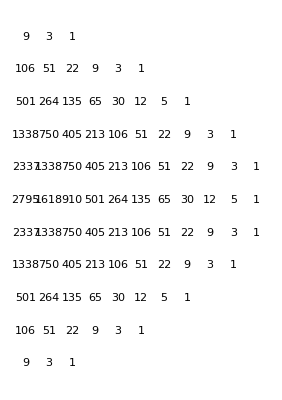

```mathematica
affinePlot[pmults]
```

```mathematica
Scan[(res[hashtable][#]=pmults[#];pmults=pmults-pmults[#]*racahMultiplicities[subs][#])&,wgs];
```

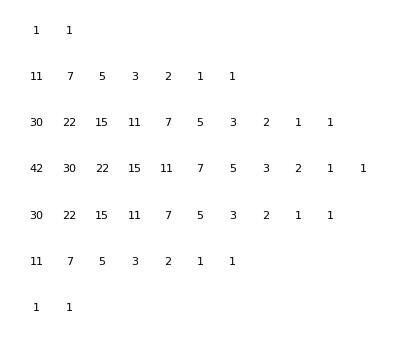

```mathematica
affinePlot[ch1]
```

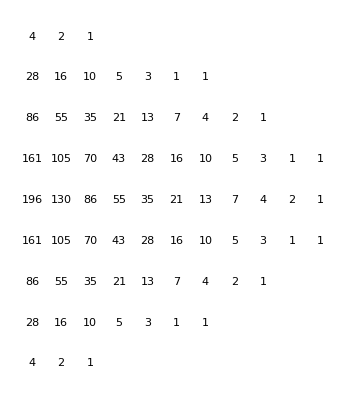

```mathematica
affinePlot[ch2]
```

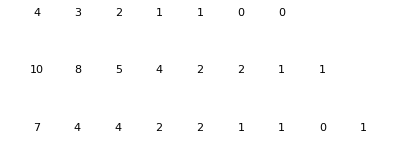

```mathematica
affinePlot[res]
```

```mathematica
rho[a1a]
```

affineWeight[1,finiteWeight[1,{1/(√2)}],2,0]

```mathematica
dynkinLabels[Subscript[D, 7]][highestRoot[Subscript[D, 7]]]
```

{0,1,0,0,0,0,0}

```mathematica
highestRoot[Subscript[D, 7]].#&/@simpleRoots[Subscript[D, 7]]
```

{0,1,0,0,0,0,0}

```mathematica
marks[OverHat[Subscript[A, 7]]]
```

{1,1,1,1,1,1,1,1}

```mathematica
simpleRoots[Subscript[G, 2]]
```

{finiteWeight[3,{1/(√3),-1/(√3),0}],finiteWeight[3,{-2/(√3),1/(√3),1/(√3)}]}

```mathematica
Plus@@marks[OverHat[Subscript[D, 8]]]
```

14

```mathematica
Plus@@comarks[OverHat[Subscript[G, 2]]]
```

4

```mathematica
1+Plus@@(2*(finiteWeight[3,{1/(√3),1/(√3),0}].#)/(#.#)&/@simpleRoots[Subscript[G, 2]])
```

2/3

```mathematica
|
```

```mathematica
conformalWeight[OverHat[Subscript[A, 2]]][1,0,0]
```

affineRootSystem[2,finiteRootSystem[2,3,{finiteWeight[3,{1,-1,0}],finiteWeight[3,{0,1,-1}]}],affineWeight[3,finiteWeight[3,{-1,0,1}],0,1],{affineWeight[3,finiteWeight[3,{1,-1,0}],0,0],affineWeight[3,finiteWeight[3,{0,1,-1}],0,0]}].(affineRootSystem[2,finiteRootSystem[2,3,{finiteWeight[3,{1,-1,0}],finiteWeight[3,{0,1,-1}]}],affineWeight[3,finiteWeight[3,{-1,0,1}],0,1],{affineWeight[3,finiteWeight[3,{1,-1,0}],0,0],affineWeight[3,finiteWeight[3,{0,1,-1}],0,0]}]+affineWeight[1,finiteWeight[1,{√2}],4,0])/(2 (2+level[affineRootSystem[2,finiteRootSystem[2,3,{finiteWeight[3,{1,-1,0}],finiteWeight[3,{0,1,-1}]}],affineWeight[3,finiteWeight[3,{-1,0,1}],0,1],{affineWeight[3,finiteWeight[3,{1,-1,0}],0,0],affineWeight[3,finiteWeight[3,{0,1,-1}],0,0]}]]))[1,0,0]

```mathematica
conformalWeight[hw1_]:=hw1.(hw1+2*rho[a1a])/(2*(level[hw1]+2))
```

```mathematica
conformalWeight[weight[a1a][1,0]]+conformalWeight[weight[a1a][0,1]]-conformalWeight[weight[a1a][2,0]]
```

1/4

```mathematica
ch3=ch1*ch2
```

$Aborted

```mathematica
c1=character[makeIrreducibleModule[Subscript[A, 1]][2]];
c2=character[makeIrreducibleModule[Subscript[A, 1]][3]];
```

```mathematica
(c1*c2)[multiplicities]
```

{1,2,3,3,2,1}

```mathematica
c3=makeFormalElement@@Transpose[Flatten[Outer[{#1+#2,c1[#1]*c2[#2]}&,c1[weights],c2[weights]],1]]
```

formalElement[Affine`Private`table$1533]

```mathematica
c3[multiplicities]
```

{1,3,2,3,1,2}